```mathematica
Show[
ParametricPlot3D[{(7-h)/7 2Cos[θ],(7-h)/7 2Sin[θ],h},{θ,0,2π},{h,0,7},PlotStyle->Green],
ParametricPlot3D[{2/7 (7-θ/(4 π)) Cos[θ],2/7 (7-θ/(4 π)) Sin[θ],θ/(4 π)},{θ,0,28π},PlotStyle->{Red,Thickness[0.02]}]
]
```

-Graphics3D-

```mathematica
frames=Table[Grid[{{
Show[
ParametricPlot[{Cos[6π t],Sin[8π t]},{t,0,1}],
Graphics[{PointSize[0.05],Red,Point[{Cos[6π s],Sin[8π s]}]}]
],
Show[
Plot[Norm[{-6 π Sin[6 π t],8 π Cos[8 π t]}],{t,0,1}],
Graphics[{PointSize[0.05],Red,Point[{s,Norm[{-6 π Sin[6 π s],8 π Cos[8 π s]}]}]}]
]}}],
{s,0,199/200,1/200}
];
```

```mathematica
D[{Cos[6π t],Sin[8π t]},t]
```

{-6 π Sin[6 π t],8 π Cos[8 π t]}

```mathematica
Export["/Users/local_pkagey/Desktop/frames.gif",frames]
```

/Users/local_pkagey/Desktop/frames.gif

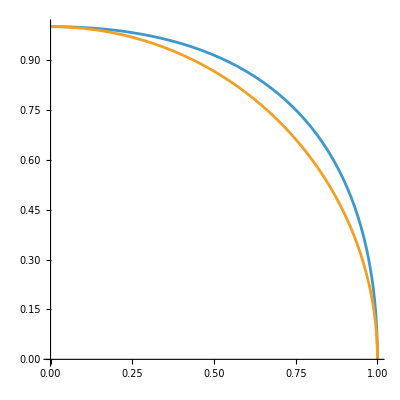

```mathematica
ParametricPlot[{(1-t)^2{1,0}+2t(1-t){1,1}+t^2{0,1},{Cos[π/2 t],Sin[π/2 t]}},{t,0,1}]
D[(1-t)^2{1,0}+2t(1-t){1,1}+t^2{0,1},t]
```

```mathematica
2NIntegrate[Norm[{-2 t,2 (1-t)}],{t,0,1}]
```

3.24645

```mathematica
treePlot=ParametricPlot3D[{2/7 (7-h) Cos[t],2/7 (7-h) Sin[t],h},{t,0,2 Pi},{h,0,7},PlotStyle->Green];
ornament1=Graphics3D[{Red,Sphere[{1,0,3.5},0.2]}];
ornament2=Graphics3D[{Blue,Sphere[{0,1,3.5},0.2]}];
Show[treePlot,ornament1, ornament2]
```

-Graphics3D-

-Graphics3D-